# Coronavirus (COVID-19)

## Initialization code

```mathematica
dispFrame[data_, title_:"Title", size_:{Automatic,300}]:= Labeled[Framed[Pane[Grid[data], Scrollbars->True, ImageSize->size]], title, Top];

isoHeat={{0,0,0},{0.027065,0.00002143,0},{0.052054,0.000074728,0},{0.071511,0.00013914,0},{0.08742,0.0002088,0},{0.10109,0.00028141,0},{0.11337,0.000356,2.4266*^-17},{0.12439,0.00043134,3.3615*^-17},{0.13463,0.00050796,2.1604*^-17},{0.14411,0.0005856,0},{0.15292,0.00070304,0},{0.16073,0.0013432,0},{0.16871,0.0014516,0},{0.17657,0.0012408,0},{0.18364,0.0015336,0},{0.19052,0.0017515,0},{0.19751,0.0015146,0},{0.20401,0.0015249,0},{0.20994,0.0019639,0},{0.21605,0.002031,0},{0.22215,0.0017559,0},{0.22808,0.001546,0.000018755},{0.23378,0.0016315,0.000035012},{0.23955,0.0017194,0.000033352},{0.24531,0.0018097,0.000018559},{0.25113,0.0019038,0.000019139},{0.25694,0.0020015,0.000035308},{0.26278,0.0021017,0.000032613},{0.26864,0.0022048,0.000020338},{0.27451,0.0023119,0.000022453},{0.28041,0.0024227,0.000036003},{0.28633,0.0025363,0.000029817},{0.29229,0.0026532,0.000019559},{0.29824,0.0027747,0.000027666},{0.30423,0.0028999,0.000035752},{0.31026,0.0030279,0.000023231},{0.31628,0.0031599,0.000012902},{0.32232,0.0032974,0.000032915},{0.32838,0.0034379,0.000032803},{0.33447,0.0035819,0.000020757},{0.34057,0.003731,0.000023831},{0.34668,0.0038848,0.00003502},{0.35283,0.0040418,0.000024468},{0.35897,0.0042032,0.000011444},{0.36515,0.0043708,0.000032793},{0.37134,0.0045418,0.00003012},{0.37756,0.0047169,0.000014846},{0.38379,0.0048986,0.00002796},{0.39003,0.0050848,0.000032782},{0.3963,0.0052751,0.000019244},{0.40258,0.0054715,0.000022667},{0.40888,0.0056736,0.000033223},{0.41519,0.0058798,0.00002159},{0.42152,0.0060922,0.000018214},{0.42788,0.0063116,0.000032525},{0.43424,0.0065353,0.000022247},{0.44062,0.006765,0.000015852},{0.44702,0.0070024,0.000031769},{0.45344,0.0072442,0.000021245},{0.45987,0.0074929,0.000015726},{0.46631,0.0077499,0.000030976},{0.47277,0.0080108,0.000018722},{0.47926,0.0082789,0.000019285},{0.48574,0.0085553,0.000030063},{0.49225,0.0088392,0.000014313},{0.49878,0.0091356,0.000023404},{0.50531,0.0094374,0.000028099},{0.51187,0.0097365,6.4695*^-6},{0.51844,0.010039,0.000025791},{0.52501,0.010354,0.000024393},{0.53162,0.010689,0.000016037},{0.53825,0.011031,0.000027295},{0.54489,0.011393,0.000015848},{0.55154,0.011789,0.000023111},{0.55818,0.012159,0.000025416},{0.56485,0.012508,0.000015064},{0.57154,0.012881,0.00002541},{0.57823,0.013283,0.000016166},{0.58494,0.013701,0.00002263},{0.59166,0.014122,0.000023316},{0.59839,0.014551,0.000019432},{0.60514,0.014994,0.000024323},{0.6119,0.01545,0.000013929},{0.61868,0.01592,0.000021615},{0.62546,0.016401,0.000015846},{0.63226,0.016897,0.000020838},{0.63907,0.017407,0.000019549},{0.64589,0.017931,0.000020961},{0.65273,0.018471,0.000020737},{0.65958,0.019026,0.000020621},{0.66644,0.019598,0.000020675},{0.67332,0.020187,0.000020301},{0.68019,0.020793,0.000020029},{0.68709,0.021418,0.000020088},{0.69399,0.022062,0.000019102},{0.70092,0.022727,0.000019662},{0.70784,0.023412,0.000017757},{0.71478,0.024121,0.000018236},{0.72173,0.024852,0.000014944},{0.7287,0.025608,2.0245*^-6},{0.73567,0.02639,1.5013*^-7},{0.74266,0.027199,0},{0.74964,0.028038,0},{0.75665,0.028906,0},{0.76365,0.029806,0},{0.77068,0.030743,0},{0.77771,0.031711,0},{0.78474,0.032732,0},{0.79179,0.033741,0},{0.79886,0.034936,0},{0.80593,0.036031,0},{0.81299,0.03723,0},{0.82007,0.038493,0},{0.82715,0.039819,0},{0.83423,0.041236,0},{0.84131,0.042647,0},{0.84838,0.044235,0},{0.85545,0.045857,0},{0.86252,0.047645,0},{0.86958,0.049578,0},{0.87661,0.051541,0},{0.88365,0.053735,0},{0.89064,0.056168,0},{0.89761,0.058852,0},{0.90451,0.061777,0},{0.91131,0.065281,0},{0.91796,0.069448,0},{0.92445,0.074684,0},{0.93061,0.08131,0},{0.93648,0.088878,0},{0.94205,0.097336,0},{0.9473,0.10665,0},{0.9522,0.1166,0},{0.95674,0.12716,0},{0.96094,0.13824,0},{0.96479,0.14963,0},{0.96829,0.16128,0},{0.97147,0.17303,0},{0.97436,0.18489,0},{0.97698,0.19672,0},{0.97934,0.20846,0},{0.98148,0.22013,0},{0.9834,0.23167,0},{0.98515,0.24301,0},{0.98672,0.25425,0},{0.98815,0.26525,0},{0.98944,0.27614,0},{0.99061,0.28679,0},{0.99167,0.29731,0},{0.99263,0.30764,0},{0.9935,0.31781,0},{0.99428,0.3278,0},{0.995,0.33764,0},{0.99564,0.34735,0},{0.99623,0.35689,0},{0.99675,0.3663,0},{0.99722,0.37556,0},{0.99765,0.38471,0},{0.99803,0.39374,0},{0.99836,0.40265,0},{0.99866,0.41145,0},{0.99892,0.42015,0},{0.99915,0.42874,0},{0.99935,0.43724,0},{0.99952,0.44563,0},{0.99966,0.45395,0},{0.99977,0.46217,0},{0.99986,0.47032,0},{0.99993,0.47838,0},{0.99997,0.48638,0},{1,0.4943,0},{1,0.50214,0},{1,0.50991,0.000012756},{1,0.51761,0.000045388},{1,0.52523,0.000096977},{1,0.5328,0.00016858},{1,0.54028,0.0002582},{1,0.54771,0.00036528},{1,0.55508,0.00049276},{1,0.5624,0.00063955},{1,0.56965,0.00080443},{1,0.57687,0.00098902},{1,0.58402,0.0011943},{1,0.59113,0.0014189},{1,0.59819,0.0016626},{1,0.60521,0.0019281},{1,0.61219,0.0022145},{1,0.61914,0.0025213},{1,0.62603,0.0028496},{1,0.6329,0.0032006},{1,0.63972,0.0035741},{1,0.64651,0.0039701},{1,0.65327,0.0043898},{1,0.66,0.0048341},{1,0.66669,0.005303},{1,0.67336,0.0057969},{1,0.67999,0.006317},{1,0.68661,0.0068648},{1,0.69319,0.0074406},{1,0.69974,0.0080433},{1,0.70628,0.0086756},{1,0.71278,0.0093486},{1,0.71927,0.010023},{1,0.72573,0.010724},{1,0.73217,0.011565},{1,0.73859,0.012339},{1,0.74499,0.01316},{1,0.75137,0.014042},{1,0.75772,0.014955},{1,0.76406,0.015913},{1,0.77039,0.016915},{1,0.77669,0.017964},{1,0.78298,0.019062},{1,0.78925,0.020212},{1,0.7955,0.021417},{1,0.80174,0.02268},{1,0.80797,0.024005},{1,0.81418,0.025396},{1,0.82038,0.026858},{1,0.82656,0.028394},{1,0.83273,0.030013},{1,0.83889,0.031717},{1,0.84503,0.03348},{1,0.85116,0.035488},{1,0.85728,0.037452},{1,0.8634,0.039592},{1,0.86949,0.041898},{1,0.87557,0.044392},{1,0.88165,0.046958},{1,0.88771,0.04977},{1,0.89376,0.052828},{1,0.8998,0.056209},{1,0.90584,0.059919},{1,0.91185,0.063925},{1,0.91783,0.068579},{1,0.92384,0.073948},{1,0.92981,0.080899},{1,0.93576,0.090648},{1,0.94166,0.10377},{1,0.94752,0.12051},{1,0.9533,0.14149},{1,0.959,0.1672},{1,0.96456,0.19823},{1,0.96995,0.23514},{1,0.9751,0.2786},{1,0.97992,0.32883},{1,0.98432,0.38571},{1,0.9882,0.44866},{1,0.9915,0.51653},{1,0.99417,0.58754},{1,0.99625,0.65985},{1,0.99778,0.73194},{1,0.99885,0.80259},{1,0.99953,0.87115},{1,0.99989,0.93683},{1,1,1}};

Clear[isoHcf]
isoHcf[col_]:=Blend[RGBColor[#]&/@Reverse[isoHeat],col];
```

```mathematica
importSeq[id_]:=Import[StringJoin["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=", id],{"PDB","Sequence"}];

importCoords[id_]:=Import[StringJoin["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=", id],{"PDB","ResidueCoordinates"}];

calculateCentroids[coords_]:=  Total[#]/Length[#]&/@coords;

showCentroids[centroids_]:=dispFrame[Prepend[centroids, {"X", "Y", "Z"}], "Centroids"];

generateDistanceMatrix[centroids_]:=0.01 DistanceMatrix[centroids];

visualizeDistanceMatrix[matrix_]:=
Module[{range},
range=Range[0, Length[matrix],20];
ArrayPlot[matrix,
Frame->True,
ColorFunction->isoHcf,
ImageSize->Full,
FrameTicksStyle->Directive[FontSize->12],
FrameTicks->{{range, None}, {None, range}},
FrameLabel->{{None, Style["Residue Sequence",12]},
{Style["Residue Sequence", 12], None}},
PlotLegends->
{Placed[BarLegend[{isoHcf[#]&,{0,Max[matrix]}},
LabelStyle->Directive[Black,FontSize->12],
LegendLabel->"Distance (Angstroms)",
LegendMarkerSize->400,
LegendLayout->"Column"],{{1,1},{0,1}}]}]];
```

## Introduction

We recently saw COVID-19 emerge. Six kinds of human COVs have been previously identified. [Insert Atomic Hands photo].

Classified into three groups, initially based on antigenic relationships of the spike, membrane, and nucleocapsid proteins and now re-enforced by viral genetic phylogeny.

Group 1 (alphacoronavirus)

HCoV-NL63

First identified in the Netherlands in 2004

HCoV-229E

Group 2 (betacoronavirus)

HCoV-HKU1

HCoV-OC43

SARS-CoV-2, or coronavirus disease of 2019 (COVID-19)

First reported in Wuhan, China in November 2003.

70% genetic similarity to SARS-CoV.

MERS-CoV, or Middle East respiratory syndrome (MERS)

First reported in Saudi Arabia in 2012.

SARS-CoV, or severe acute respiratory syndrome (SARS)

First reported in the Guangdong province in southern China in February 2003.

Coronavirus spike glycoproteins mediate receptor binding, membrane fusion, and virus entry and determine host range. Betacoronavirus in group A use the N-terminal domain (NTD) of S protein to bind to its receptors, where the beta COVs SARS in group B and MERS in group C and several alpha COVs use the downstream C domain in their S proteins to recognize their receptor proteins.

HKU1 receptor-binding domain is located in the C domain.

PDBU codes:

```mathematica
covid19 = "6VSB";
hcovoc43="6OHW";
sarscov="5XLR";
hcovhku1 ="3D23"; 
merscov="6BI8";
hcov229e="6U7H";
hcovnl63="5GWY";
```

## Sequence analysis

### COVID-19

```mathematica
covid19SeqArr =importSeq[covid19]
```

{AYTNSFTRGVYYPDKVFRSSVLHSTQDLFLPFFSNVTWFH,FDNPVLPFNDGVYFAST,NIIRGWIFGTTLDSKTQSLLIVNNATNVVIKVCEFQFCNDPFLG,EFRVYSSANNCTFEYVSQPFL,KNLREFVFKNIDGYFKIYSKHTPINLVRDLPQGFSALEPLVDLPIGINITRFQTLLALHR,GAAAYYVGYLQPRTFLLKYNENGTITDAVDCALDPLSETKCTLKSFTVEKGIYQTSNFRVQPTESIVR,LCPFGEVFNATRFASVYAWNRKRISNCVADYSVLYNSASFSTFKCYGVSPTKLNDLCFTNVYADSFVIRGDEVRQIAPGQTGKIADYNYKLPDDFTGCVIAWNSNNLDS,YNYLYR,PLQSYGFQPT,VGYQPYRVVVLSFELLHAPATVCGPKKSTNLVKNKCVNFNFNGLTGTGVLTESNKKFLPFQQFGRDIADTTDAVRDPQTLEILDITPCSFGGVSVITPGTNTSNQVAVLYQDVNCTEV,SNVFQTRAGCLIGAEHVNNSYECDIPIGAGICA,VASQSIIAYTMSLGAENSVAYSNNSIAIPTNFTISVTTEILPVSMTKTSVDCTMYICGDSTECSNLLLQYGSFCTQLNRALTGIAVEQDKNTQEVFAQVKQIYKTPPIKDFGGFNFSQILPDPSK,RSFIEDLLFNKVTL,QKFNGLTVLPPLLTDEMIAQYTSALLAGTITSGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKLIANQFNSAIGKIQDSLSSTASALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDPPEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQSAPHGVVFLHVTYVPAQEKNFTTAPAICHDGKAHFPREGVFVSNGTHWFVTQRNFYEPQIITTDNTFVSGNCDVVIGIVNNTVYDPLQPELD,XXXXXXXXXXXXXXXXXXX,AYTNSFTRGVYYPDKVFRSSVLHSTQDLFLPFFSNVTWFH,NPVLPFNDGVYFASTEKSNIIRGWIFGTTLDSKTQSLLIVNNATNVVIKVCEFQFCNDPFL,SEFRVYSSANNCTFEYVSQPFL,KNLREFVFKNIDGYFKIYSKHTP,PQGFSALEPLVDLPIGINITRFQTLL,AAYYVGYLQPRTFLLKYNENGTITDAVDCALDPLSETKCTLKSFTVEKGIYQTSNFRVQPTESIVRFPNITNLCPFGEVFNATRFASVYAWNRKRISNCVADYSVLYNSASFSTFKCYGVSPTKLNDLCFTNVYADSFVIRGDEVRQIAPGQTGKIADYNYKLPDDFTGCVIAWNSNNLDS,YNYLYR,NLKPFERDISTEIY,NCYFPLQSYGFQPT,VGYQPYRVVVLSFELLHAPATVCGPKKSTNLVKNKCVNFNFNGLTGTGVLTESNKKFLPFQQFGRDIADTTDAVRDPQTLEILDITPCSFGGVSVITPGTNTSNQVAVLYQDVNCTEV,TGSNVFQTRAGCLIGAEHVNNSYECDIPIGAGICA,VASQSIIAYTMSLGAENSVAYSNNSIAIPTNFTISVTTEILPVSMTKTSVDCTMYICGDSTECSNLLLQYGSFCTQLNRALTGIAVEQDKNTQEVFAQVKQIYKTPPIKDFGGFNFSQILPDPSK,RSFIEDLLFNKVTL,QKFNGLTVLPPLLTDEMIAQYTSALLAGTITSGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKLIANQFNSAIGKIQDSLSSTASALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDPPEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQSAPHGVVFLHVTYVPAQEKNFTTAPAICHDGKAHFPREGVFVSNGTHWFVTQRNFYEPQIITTDNTFVSGNCDVVIGIVNNTVYDPLQPELD,XXXXXXXXXXXXXXXXXXXXX,AYTNSFTRGVYYPDKVFRSSVLHSTQDLFLPFFSNVTWFH,DNPVLPFNDGVYFAST,NIIRGWIFGTTLDSKTQSLLIVNNATNVVIKVCEFQFCNDPF,FRVYSSANNCTFEYVSQPFL,KNLREFVFKNIDGYFKIYSKHTPINLVRDLPQGFSALEPLVDLPIGINITRFQTLLALH,GAAAYYVGYLQPRTFLLKYNENGTITDAVDCALDPLSETKCTLKSFTVEKGIYQTSNFRVQPTESIVRFPNITNLCPFGEVFNATRFASVYAWNRKRISNCVADYSVLYNSASFSTFKCYGVSPTKLNDLCFTNVYADSFVIRGDEVRQIAPGQTGKIADYNYKLPDDFTGCVIAWNSNNLDS,YNYLYR,NLKPFERDISTE,NCYFPLQSYGFQ,VGYQPYRVVVLSFELLHAPATVCGPKKSTNLVKNKCVNFNFNGLTGTGVLTESNKKFLPFQQFGRDIADTTDAVRDPQTLEILDITPCSFGGVSVITPGTNTSNQVAVLYQDVNCTEV,NVFQTRAGCLIGAEHVNNSYECDIPIGAGICA,VASQSIIAYTMSLGAENSVAYSNNSIAIPTNFTISVTTEILPVSMTKTSVDCTMYICGDSTECSNLLLQYGSFCTQLNRALTGIAVEQDKNTQEVFAQVKQIYKTPPIKDFGGFNFSQILPDPSK,RSFIEDLLFNKVTL,QKFNGLTVLPPLLTDEMIAQYTSALLAGTITSGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKLIANQFNSAIGKIQDSLSSTASALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDPPEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQSAPHGVVFLHVTYVPAQEKNFTTAPAICHDGKAHFPREGVFVSNGTHWFVTQRNFYEPQIITTDNTFVSGNCDVVIGIVNNTVYDPLQPELD,XXXXXXXXXXXXXXXXXXXXX}

After looking at the sequence tab in its page on PDB, we want to join [5] and [6].

```mathematica
covid19Seq=StringJoin[covid19SeqArr[[5]],covid19SeqArr[[6]]]
```

KNLREFVFKNIDGYFKIYSKHTPINLVRDLPQGFSALEPLVDLPIGINITRFQTLLALHRGAAAYYVGYLQPRTFLLKYNENGTITDAVDCALDPLSETKCTLKSFTVEKGIYQTSNFRVQPTESIVR

From https://www.ncbi.nlm.nih.gov/nuccore/NC_045512.2?report=genbank

```mathematica
covid19ncbi="NC_045512.2";
```

```mathematica
importGene[id_]:=Import[StringJoin["https://eutils.ncbi.nlm.nih.gov/entrez/eutils?db_xref=\"GeneID:43740578\"", id]];
```

```mathematica
importGene[covid19ncbi]
```

FetchURL::httperr: The request to URL https://eutils.ncbi.nlm.nih.gov/entrez/eutils?db_xref="GeneID:43740578"NC_045512.2 was not successful. The server returned the HTTP status code 404 ("Not Found").

$Failed

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/briennakh/Documents/Coursework/PhD (U of M)/projects/covid-19

```mathematica
covid19Seq=Import["data/NC_045512.2.fasta","FASTA"];
StringLength[covid19Seq]
```

{29903}

```mathematica
partitions=Partition[Flatten[StringSplit[covid19Seq,""]],UpTo[400]]
```

{1}
 |  |  |  |

```mathematica
Last[partitions]
```

{G,T,C,T,A,C,T,C,T,T,G,T,G,C,A,G,A,A,T,G,A,A,T,T,C,T,C,G,T,A,A,C,T,A,C,A,T,A,G,C,A,C,A,A,G,T,A,G,A,T,G,T,A,G,T,T,A,A,C,T,T,T,A,A,T,C,T,C,A,C,A,T,A,G,C,A,A,T,C,T,T,T,A,A,T,C,A,G,T,G,T,G,T,A,A,C,A,T,T,A,G,G,G,A,G,G,A,C,T,T,G,A,A,A,G,A,G,C,C,A,C,C,A,C,A,T,T,T,T,C,A,C,C,G,A,G,G,C,C,A,C,G,C,G,G,A,G,T,A,C,G,A,T,C,G,A,G,T,G,T,A,C,A,G,T,G,A,A,C,A,A,T,G,C,T,A,G,G,G,A,G,A,G,C,T,G,C,C,T,A,T,A,T,G,G,A,A,G,A,G,C,C,C,T,A,A,T,G,T,G,T,A,A,A,A,T,T,A,A,T,T,T,T,A,G,T,A,G,T,G,C,T,A,T,C,C,C,C,A,T,G,T,G,A,T,T,T,T,A,A,T,A,G,C,T,T,C,T,T,A,G,G,A,G,A,A,T,G,A,C,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A}

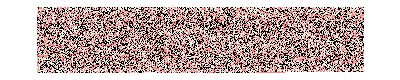

```mathematica
ArrayPlot[Partition[Flatten[StringSplit[covid19Seq,""]],UpTo[400]],
ColorRules->{"A"->Pink,"C"->LightPink, "T"->Black,"G"-> LightGreen},
ImageSize->Full]
```

https://www.ncbi.nlm.nih.gov/nuccore/667489388
MERS-CoV

```mathematica
merscovSeq=Import["data/mers-cov.fasta","FASTA"];
StringLength[merscovSeq]
```

{30119}

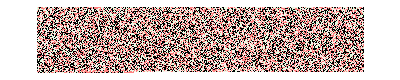

```mathematica
ArrayPlot[Partition[Flatten[StringSplit[merscovSeq,""]],UpTo[400]],
ColorRules->{"A"->Pink,"C"->LightPink, "T"->Black,"G"-> LightGreen},
ImageSize->Full]
```

SARS https://www.ncbi.nlm.nih.gov/nuccore/30271926

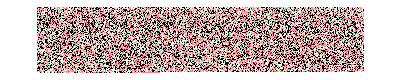

```mathematica
sarscovSeq=Import["data/sars-cov.fasta","FASTA"];
ArrayPlot[Partition[Flatten[StringSplit[sarscovSeq,""]],UpTo[400]],
ColorRules->{"A"->Pink,"C"->LightPink, "T"->Black,"G"-> LightGreen},
ImageSize->Full]
```

COMPLETE GENOME.

### SARS-CoV

```mathematica
sarscovSeqArr=importSeq[sarscov]
```

{HTSSMRGVYYPDEIFRSDTLYLTQDLFLPFYSNVTGFHT,GNPVIPFKDGIYFAATEKSNVVRGWVFGSTMNNKSQSVIIINNSTNVVIRACNFE,HTMIFDNAFNCTFEYISDA,KHLREFVFKNKDGFLYVYKGYQPIDVVRDLPSGFNTLKPIFKLPLGINITNFRAILTAF,AAAYFVGYLKPTTFMLKYDENGTITDAVDCSQNPLAELKCSVKSFEIDKGIYQTSNFRVVPSGDVVRFPNITNLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRYLRHGKLRPFERDISNVPFSPDGKPCTPPALNCYWPLNDYGFYTTTGIGYQPYRVVVLSFELLNAPATVCGPKLSTDLIKNQCVNFNFNGLTGTGVLTPSSKRFQPFQQFGRDVSDFTDSVRDPKTSEILDISPCSFGGVSVITPGTNASSEVAVLYQDVNCTDVSTAIHADQLTPAWRIYSTGNNVFQTQAGCLIGAEHVDTSYECDIPIGAGICASY,VAYTMSLGADSSIAYSNNTIAIPTNFSISITTEVMPVSMAKTSVDCNMYICGDSTECANLLLQYGSFCTQLNRALSGIAAEQDRNTREVFAQVKQMYKTPTLKYFGGFNFSQILPDPLKPTKRSFIEDLLFNKVTLADAGFMKQYGECL,ICAQKFNGLTVLPPLLTDDMIAAYTAALVSGTATAGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKQIANQFNKAISQIQESLTTTSTALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDKVEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQAAPHGVVFLHVTYVPSQERNFTTAPAICHEGKAYFPREGVFVFNGTSWFITQRNFFSPQIITTDNTFVSGNCDVVIGIINNTVY,HTSSMRGVYYPDEIFRSDTLYLTQDLFLPFYSNVTGFHT,GNPVIPFKDGIYFAATEKSNVVRGWVFGSTMNNKSQSVIIINNSTNVVIRACNFE,HTMIFDNAFNCTFEYISDA,KHLREFVFKNKDGFLYVYKGYQPIDVVRDLPSGFNTLKPIFKLPLGINITNFRAILTAF,AAAYFVGYLKPTTFMLKYDENGTITDAVDCSQNPLAELKCSVKSFEIDKGIYQTSNFRVVPSGDVVRFPNITNLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRYLRHGKLRPFERDISNVPFSPDGKPCTPPALNCYWPLNDYGFYTTTGIGYQPYRVVVLSFELLNAPATVCGPKLSTDLIKNQCVNFNFNGLTGTGVLTPSSKRFQPFQQFGRDVSDFTDSVRDPKTSEILDISPCSFGGVSVITPGTNASSEVAVLYQDVNCTDVSTAIHADQLTPAWRIYSTGNNVFQTQAGCLIGAEHVDTSYECDIPIGAGICASY,VAYTMSLGADSSIAYSNNTIAIPTNFSISITTEVMPVSMAKTSVDCNMYICGDSTECANLLLQYGSFCTQLNRALSGIAAEQDRNTREVFAQVKQMYKTPTLKYFGGFNFSQILPDPLKPTKRSFIEDLLFNKVTLADAGFMKQYGECL,ICAQKFNGLTVLPPLLTDDMIAAYTAALVSGTATAGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKQIANQFNKAISQIQESLTTTSTALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDKVEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQAAPHGVVFLHVTYVPSQERNFTTAPAICHEGKAYFPREGVFVFNGTSWFITQRNFFSPQIITTDNTFVSGNCDVVIGIINNTVY,HTSSMRGVYYPDEIFRSDTLYLTQDLFLPFYSNVTGFHT,GNPVIPFKDGIYFAATEKSNVVRGWVFGSTMNNKSQSVIIINNSTNVVIRACNFE,HTMIFDNAFNCTFEYISDA,KHLREFVFKNKDGFLYVYKGYQPIDVVRDLPSGFNTLKPIFKLPLGINITNFRAILTAF,AAAYFVGYLKPTTFMLKYDENGTITDAVDCSQNPLAELKCSVKSFEIDKGIYQTSNFRVVPSGDVVRFPNITNLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRYLRHGKLRPFERDISNVPFSPDGKPCTPPALNCYWPLNDYGFYTTTGIGYQPYRVVVLSFELLNAPATVCGPKLSTDLIKNQCVNFNFNGLTGTGVLTPSSKRFQPFQQFGRDVSDFTDSVRDPKTSEILDISPCSFGGVSVITPGTNASSEVAVLYQDVNCTDVSTAIHADQLTPAWRIYSTGNNVFQTQAGCLIGAEHVDTSYECDIPIGAGICASY,VAYTMSLGADSSIAYSNNTIAIPTNFSISITTEVMPVSMAKTSVDCNMYICGDSTECANLLLQYGSFCTQLNRALSGIAAEQDRNTREVFAQVKQMYKTPTLKYFGGFNFSQILPDPLKPTKRSFIEDLLFNKVTLADAGFMKQYGECL,ICAQKFNGLTVLPPLLTDDMIAAYTAALVSGTATAGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKQIANQFNKAISQIQESLTTTSTALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDKVEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQAAPHGVVFLHVTYVPSQERNFTTAPAICHEGKAYFPREGVFVFNGTSWFITQRNFFSPQIITTDNTFVSGNCDVVIGIINNTVY}

After looking at the sequence tab in its page on PDB, we want [5].

```mathematica
sarscovSeq=sarscovSeqArr[[5]]
```

AAAYFVGYLKPTTFMLKYDENGTITDAVDCSQNPLAELKCSVKSFEIDKGIYQTSNFRVVPSGDVVRFPNITNLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRYLRHGKLRPFERDISNVPFSPDGKPCTPPALNCYWPLNDYGFYTTTGIGYQPYRVVVLSFELLNAPATVCGPKLSTDLIKNQCVNFNFNGLTGTGVLTPSSKRFQPFQQFGRDVSDFTDSVRDPKTSEILDISPCSFGGVSVITPGTNASSEVAVLYQDVNCTDVSTAIHADQLTPAWRIYSTGNNVFQTQAGCLIGAEHVDTSYECDIPIGAGICASY

### HCoV-OC43

```mathematica
protein=
```

### sdfsdf

```mathematica
seq=importSeq[covid19];
StringLength[seq[[1]]]
StringLength[seq[[2]]]
seq[[1]]
```

From NCBI:

```mathematica
ncbiSeq="MFVFLVLLPLVSSQCVNLTTRTQLPPAYTNSFTRGVYYPDKVFRSSVLHSTQDLFLPFFSNVTWFHAIHVSGTNGTKRFDNPVLPFNDGVYFASTEKSNIIRGWIFGTTLDSKTQSLLIVNNATNVVIKVCEFQFCNDPFLGVYYHKNNKSWMESEFRVYSSANNCTFEYVSQPFLMDLEGKQGNFKNLREFVFKNIDGYFKIYSKHTPINLVRDLPQGFSALEPLVDLPIGINITRFQTLLALHRSYLTPGDSSSGWTAGAAAYYVGYLQPRTFLLKYNENGTITDAVDCALDPLSETKCTLKSFTVEKGIYQTSNFRVQPTESIVRFPNITNLCPFGEVFNATRFASVYAWNRKRISNCVADYSVLYNSASFSTFKCYGVSPTKLNDLCFTNVYADSFVIRGDEVRQIAPGQTGKIADYNYKLPDDFTGCVIAWNSNNLDSKVGGNYNYLYRLFRKSNLKPFERDISTEIYQAGSTPCNGVEGFNCYFPLQSYGFQPTNGVGYQPYRVVVLSFELLHAPATVCGPKKSTNLVKNKCVNFNFNGLTGTGVLTESNKKFLPFQQFGRDIADTTDAVRDPQTLEILDITPCSFGGVSVITPGTNTSNQVAVLYQDVNCTEVPVAIHADQLTPTWRVYSTGSNVFQTRAGCLIGAEHVNNSYECDIPIGAGICASYQTQTNSPRRARSVASQSIIAYTMSLGAENSVAYSNNSIAIPTNFTISVTTEILPVSMTKTSVDCTMYICGDSTECSNLLLQYGSFCTQLNRALTGIAVEQDKNTQEVFAQVKQIYKTPPIKDFGGFNFSQILPDPSKPSKRSFIEDLLFNKVTLADAGFIKQYGDCLGDIAARDLICAQKFNGLTVLPPLLTDEMIAQYTSALLAGTITSGWTFGAGAALQIPFAMQMAYRFNGIGVTQNVLYENQKLIANQFNSAIGKIQDSLSSTASALGKLQDVVNQNAQALNTLVKQLSSNFGAISSVLNDILSRLDKVEAEVQIDRLITGRLQSLQTYVTQQLIRAAEIRASANLAATKMSECVLGQSKRVDFCGKGYHLMSFPQSAPHGVVFLHVTYVPAQEKNFTTAPAICHDGKAHFPREGVFVSNGTHWFVTQRNFYEPQIITTDNTFVSGNCDVVIGIVNNTVYDPLQPELDSFKEELDKYFKNHTSPDVDLGDISGINASVVNIQKEIDRLNEVAKNLNESLIDLQELGKYEQYIKWPWYIWLGFIAGLIAIVMVTIMLCCMTSCCSCLKGCCSCGSCCKFDEDDSEPVLKGVKLHYT";
```

```mathematica
StringLength[sequence]
```

## Distance matrices

Here we use PDB data on the protein structure, main protease. This data consists of coordinate files for atoms in each protein, and their 3D location in space.

### COVID-19 (6VSB)

The COVID-19 structure consists of a main protease that has two chains, as well as an inhibitor. The main protease is a key coronavirus enzyme that mediates viral replication and transcription. Attached to the main protease via hydrogen bonds, the inhibitor...

Liu et al. — https://www.biorxiv.org/content/10.1101/2020.02.26.964882v2.full.pdf
crystal structure — http://www.rcsb.org/pdb/explore/remediatedSequence.do?structureId=6VSB

```mathematica
seq=importSeq["6VSB"]
```

```mathematica
seq[[31]]
```

```mathematica
covid19Coords=importCoords["6VSB"];
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[covid19Coords[[31]], covid19Coords[[32]],covid19Coords[[33]],covid19Coords[[34]],covid19Coords[[35]],covid19Coords[[36]],covid19Coords[[37]],covid19Coords[[38]],covid19Coords[[39]],covid19Coords[[40]],covid19Coords[[41]],covid19Coords[[42]],covid19Coords[[43]],covid19Coords[[44]]]]]]
```

Receptor binding domain.

```mathematica
covid19RBD="6VW1";
covid19RBDSeq=importSeq[covid19RBD];
Dimensions[covid19RBDSeq]
covid19RBDSeq
```

{10}

{STIEEQAKTFLDKFNHEAEDLFYQSSLASWNYNTNITEENVQNMNNAGDKWSAFLKEQSTLAQMYPLQEIQNLTVKLQLQALQQNGSSVLSEDKSKRLNTILNTMSTIYSTGKVCNPDNPQECLLLEPGLNEIMANSLDYNERLWAWESWRSEVGKQLRPLYEEYVVLKNEMARANHYEDYGDYWRGDYEVNGVDGYDYSRGQLIEDVEHTFEEIKPLYEHLHAYVRAKLMNAYPSYISPIGCLPAHLLGDMWGRFWTNLYSLTVPFGQKPNIDVTDAMVDQAWDAQRIFKEAEKFFVSVGLPNMTQGFWENSMLTDPGNVQKAVCHPTAWDLGKGDFRILMCTKVTMDDFLTAHHEMGHIQYDMAYAAQPFLLRNGANEGFHEAVGEIMSLSAATPKHLKSIGLLSPDFQEDNETEINFLLKQALTIVGTLPFTYMLEKWRWMVFKGEIPKDQWMKKWWEMKREIVGVVEPVPHDETYCDPASLFHVSNDYSFIRYYTRTLYQFQFQEALCQAAKHEGPLHKCDISNSTEAGQKLFNMLRLGKSEPWTLALENVVGAKNMNVRPLLNYFEPLFTWLKDQNKNSFVGWSTDWSPYA,XXXXXXXXXXXXXX,STIEEQAKTFLDKFNHEAEDLFYQSSLASWNYNTNITEENVQNMNNAGDKWSAFLKEQSTLAQMYPLQEIQNLTVKLQLQALQQNGSSVLSEDKSKRLNTILNTMSTIYSTGKVCNPDNPQECLLLEPGLNEIMANSLDYNERLWAWESWRSEVGKQLRPLYEEYVVLKNEMARANHYEDYGDYWRGDYEVNGVDGYDYSRGQLIEDVEHTFEEIKPLYEHLHAYVRAKLMNAYPSYISPIGCLPAHLLGDMWGRFWTNLYSLTVPFGQKPNIDVTDAMVDQAWDAQRIFKEAEKFFVSVGLPNMTQGFWENSMLTDPGNVQKAVCHPTAWDLGKGDFRILMCTKVTMDDFLTAHHEMGHIQYDMAYAAQPFLLRNGANEGFHEAVGEIMSLSAATPKHLKSIGLLSPDFQEDNETEINFLLKQALTIVGTLPFTYMLEKWRWMVFKGEIPKDQWMKKWWEMKREIVGVVEPVPHDETYCDPASLFHVSNDYSFIRYYTRTLYQFQFQEALCQAAKHEGPLHKCDISNSTEAGQKLFNMLRLGKSEPWTLALENVVGAKNMNVRPLLNYFEPLFTWLKDQNKNSFVGWSTDWSPYA,XXXXXXXXXXXXXXX,NLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRLFRKSNLKPFERDISTEIYQAGSTPCNGVEGFNCYFPLQSYGFQPTNGVGYQPYRVVVLSFELLNAP,TVCGP,XXX,NITNLCPFGEVFNATKFPSVYAWERKKISNCVADYSVLYNSTFFSTFKCYGVSATKLNDLCFSNVYADSFVVKGDDVRQIAPGQTGVIADYNYKLPDDFMGCVLAWNTRNIDATSTGNYNYKYRLFRKSNLKPFERDISTEIYQAGSTPCNGVEGFNCYFPLQSYGFQPTNGVGYQPYRVVVLSFE,APATVCGP,XX}

```mathematica
covid19RBDCoords=importCoords[covid19RBD];
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[covid19RBDCoords[[5]],covid19RBDCoords[[6]]]]]]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[covid19RBDCoords[[8]],covid19RBDCoords[[9]]]]]]
```

### MERS-CoV (5GMQ)

```mathematica
importSeq[merscov]
coords=importCoords[merscov];
Dimensions[coords]
```

```mathematica
fullCoords=Join[coords[[3]],coords[[5]]];
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[coords[[1]]]]]
```

```mathematica
merscovRBD="4KQZ";
merscovRBDSeq=importSeq[merscovRBD];
Dimensions[merscovRBD]
merscovRBD
```

```mathematica
merscovRBDCoords=importCoords[merscovRBD];
Dimensions[merscovRBDCoords]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[merscovRBDCoords[[1]]]]]
```

### SARS-CoV (5XLR)

http://www.rcsb.org/pdb/explore/remediatedSequence.do?structureId=5XLR

```mathematica
sarscovSeq=importSeq[sarscov];
Dimensions[sarscovSeq]
```

```mathematica
sarscovSeq
```

```mathematica
sarscovSeq[[15]]
```

```mathematica
sarscovCoords=importCoords[sarscov];
Dimensions[sarscovCoords]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[sarscovCoords[[15]],sarscovCoords[[16]],sarscovCoords[[17]],sarscovCoords[[18]],sarscovCoords[[19]],sarscovCoords[[20]],sarscovCoords[[21]]]]]]
```

Receptor binding domain only

```mathematica
sarscovRBD="2DD8";
sarscovRBDSeq=importSeq[sarscovRBD];
Dimensions[sarscovRBDSeq]
```

{6}

```mathematica
sarscovRBDSeq
```

```mathematica
sarscovRBDCoords = importCoords[sarscovRBD];
Dimensions[sarscovRBDCoords]
```

{6}

```mathematica
StringLength[sarscovRBDSeq[[1]]]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[sarscovRBDCoords[[5]]]]]
```

### HCoV-OC43 (6OHW)

View the sequence.

```mathematica
hcovoc43seq=importSeq[hcovoc43]
hcovoc43seq[[24]]
hcovoc43seq[[11]]==hcovoc43seq[[20]]
Dimensions[hcovoc43seq]
```

According to annotations and the visualization, #11 and #20 are the same.

```mathematica
hcovoc43Coords=importCoords[hcovoc43];
Dimensions[hcovoc43Coords]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[hcovoc43Coords[[20]],hcovoc43Coords[[21]],hcovoc43Coords[[22]],hcovoc43Coords[[23]],hcovoc43Coords[[24]],hcovoc43Coords[[25]],hcovoc43Coords[[26]]]]]]
```

Receptor binding domain.

```mathematica
hcovoc43RBD="4KXJ";
hcovoc43RBDSeq=importSeq[hcovoc43RBD];
Dimensions[hcovoc43RBDSeq]
hcovoc43RBDSeq
```

```mathematica
hcovoc43RBDCoords=importCoords[hcovoc43RBD];
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[hcovoc43RBDCoords[[1]],hcovoc43RBDCoords[[2]]]]]]
```

### HCoV-HKU1 (3D23)

```mathematica
hcovhku1Seq = importSeq[hcovhku1]
```

```mathematica
hcovhku1Seq[[1]]
```

```mathematica
hcovhku1Coords = importCoords[hcovhku1];
Dimensions[hcovhku1Coords]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[hcovhku1Coords[[5]]]]]
```

MLLIIFILPTTLAVIGDFNCTNFAINDLNTTVPRISEYVVDVSYGLGTYYILDRVYLNTTILFTGYFPKSGANFRDLSLKGTTYLSTLWYQKPFLSDFNNGIFSRVKNTKLYVNKTLYSEFSTIVIGSVFINNSYTIVVQPHNGVLEITACQYTMCEYPHTICKSKGSSRNESWHFDKSEPLCLFKKNFTYNVSTDWLYFHFYQERGTFYAYYADSGMPTTFLFSLYLGTLLSHYYVLPLTCNAISSNTDNETLQYWVTPLSKRQYLLKFDNRGVITNAVDCSSSFFSEIQCKTKSLLPNTGVYDLSGFTVKPVATVHRRIPDLPDCDIDKWLNNFNVPSPLNWERKIFSNCNFNLSTLLRLVHTDSFSCNNFDESKIYGSCFKSIVLDKFAIPNSRRSDLQLGSSGFLQSSNYKIDTTSSSCQLYYSLPAINVTINNYNPSSWNRRYGFNNFNLSSHSVVYSRYCFSVNNTFCPCAKPSFASSCKSHKPPSASCPIGTNYRSCESTTVLDHTDWCRCSCLPDPITAYDPRSCSQKKSLVGVGEHCAGFGVDEEKCGVLDGSYNVSCLCSTDAFLGWSYDTCVSNNRCNIFSNFILNGINSGTTCSNDLLQPNTEVFTDVCVDYDLYGITGQGIFKEVSAVYYNSWQNLLYDSNGNIIGFKDFVTNKTYNIFPCYAGRVSAAFHQNASSLALLYRNLKCSYVLNNISLTTQPYFDSYLGCVFNADNLTDYSVSSCALRMGSGFCVDYNSPSSSSSRRKRRSISASYRFVTFEPFNVSFVNDSIESVGGLYEIKIPTNFTIVGQEEFIQTNSPKVTIDCSLFVCSNYAACHDLLSEYGTFCDNINSILDEVNGLLDTTQLHVADTLMQGVTLSSNLNTNLHFDVDNINFKSLVGCLGPHCGSSSRSFFEDLLFDKVKLSDVGFVEAYNNCTGGSEIRDLLCVQSFNGIKVLPPILSESQISGYTTAATVAAMFPPWSAAAGIPFSLNVQYRINGLGVTMDVLNKNQKLIATAFNNALLSIQNGFSATNSALAKIQSVVNSNAQALNSLLQQLFNKFGAISSSLQEILSRLDALEAQVQIDRLINGRLTALNAYVSQQLSDISLVKFGAALAMEKVNECVKSQSPRINFCGNGNHILSLVQNAPYGLLFMHFSYKPISFKTVLVSPGLCISGDVGIAPKQGYFIKHNDHWMFTGSSYYYPEPISDKNVVFMNTCSVNFTKAPLVYLNHSVPKLSDFESELSHWFKNQTSIAPNLTLNLHTINATFLDLYYEMNLIQESIKSLNNSYINLKDIGTYEMYVKWPWYVWLLISFSFIIFLVLLFFICCCTGCGSACFSKCHNCCDEYGGHHDFVIKTSHDD

Receptor binding domain.

```mathematica
hcovhku1RBD="5GNB";
importSeq[hcovhku1RBD]
```

```mathematica
hcovhku1RBDCoords=importCoords[hcovhku1RBD];
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[hcovhku1RBDCoords[[1]]]]]
```

### HCoV-229E

```mathematica
importSeq[hcov229e]
```

```mathematica
coords=importCoords[hcov229e];
fullCoords=Join[coords[[2]],coords[[3]],coords[[4]]];
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[fullCoords]]]
```

Receptor binding domain.

```mathematica
hcov229eRBD="6U7E";
importSeq[hcov229eRBD]
```

```mathematica
hcov229eRBDCoords=importCoords[hcov229eRBD];
Dimensions[hcov229eRBDCoords]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[hcov229eRBDCoords[[5]],hcov229eRBDCoords[[6]]]]]]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[Join[hcov229eRBDCoords[[8]],hcov229eRBDCoords[[9]]]]]]
```

### HCoV-NL63 (5GWY)

View the sequence.

```mathematica
hcovnl63seq=importSeq[hcovnl63]
```

```mathematica
coords=importCoords[hcovnl63];
fullCoords=Join[coords[[1]],coords[[2]]]
```

```mathematica
visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[coords[[1]]]]]
```

Get receptor binding domain.

```mathematica
hcovnl63RBD="5EPW";
importSeq[hcovnl63RBD]
```

```mathematica
hcovnl63RBDCoords=importCoords[hcovnl63RBD];
```

```mathematica
hcovnl63RBDviz=visualizeDistanceMatrix[generateDistanceMatrix[calculateCentroids[hcovnl63RBDCoords[[2]]]]]
```

### Plot all

```mathematica
sarscovRBDCentroids=calculateCentroids[sarscovRBDCoords[[5]]];
covid19RBDCentroids=calculateCentroids[Join[covid19RBDCoords[[5]],covid19RBDCoords[[6]]]];
```

```mathematica
visualizeDM[minmax_]:=ArrayPlot[#,
ColorFunction->Function[x,isoHcf[Rescale[x,minmax,MinMax@#]]],
FrameTicksStyle->Directive[FontSize->12],FrameTicks->Automatic,FrameLabel->{{None,Style["Residue Sequence",12]},{Style["Residue Sequence",12],None}},ImageSize->Medium]&

barLegend[minmax_]:=BarLegend[{isoHcf[Rescale[#,minmax]]&,minmax},LabelStyle->Directive[Black,FontSize->12],LegendLabel->"Distance (Angstroms)",LegendMarkerSize->300,LegendLayout->"Column"]
```

```mathematica
centroidlists={sarscovRBDCentroids,covid19RBDCentroids};
```

```mathematica
dms=generateDistanceMatrix/@centroidlists;
```

```mathematica
minmax=MinMax[dms]
```

{0.,59.8251}

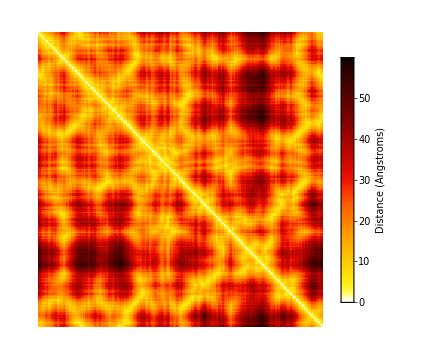
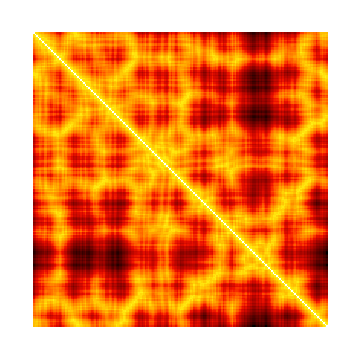

```mathematica
Legended[Row[visualizeDM[minmax]/@dms,Spacer[5]],Placed[barLegend[minmax],Right]]
```